```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
κσr = Last[Flatten[StringSplit[FileNames["KAPPA_SIGMA_R_*",NotebookDirectory[]],"_"]]];

<<Units`
<<PhysicalConstants`

β=38.6817

Print["κ/σ ratio:"]
κσr
Print["Residue-pair spring constant σ:"]
σ=0.00024
Print["Backbone spring constant κ:"]
κ=ToExpression[κσr] * σ


ToNewton=Convert[ElectronVolt/Angstrom,Newton] SI[Pico Newton]^-1;(*Converts eV/Å to pN*)ToForceDimension[f_]:=(f (κ/(2 β))^(1/2)) ToNewton;
ToDimension[η_]:=η (((κ β)/2)^(-(1/2)))(*Converts to Å*)
```

C:\Users\Hemant\Desktop\CORRECTIONSv1\Results\Collagen\collagen\kappa6

38.6817

κ/σ ratio:

22497

Residue-pair spring constant σ:

0.00024

Backbone spring constant κ:

5.39928

```mathematica
ToDimension[30.66]
```

3.00031

```mathematica
DataPlots=Table[
{
StringSplit[FileNames["Analysis*"][[i]],"_"][[2]],
path=FileNames["Analysis*"][[i]]<>"/";
ListLinePlot[{Import[path<>"new2_force.data","Table"]},PlotRange->All,PlotStyle->{Thick,ColorData[1,i]},PlotMarkers->{"●"}]
}
,{i,1,Length[FileNames["Analysis*"]]}
];
```

Import::nffil: File not found during Import.

General::stop: Further output of Import :: nffil will be suppressed during this calculation.

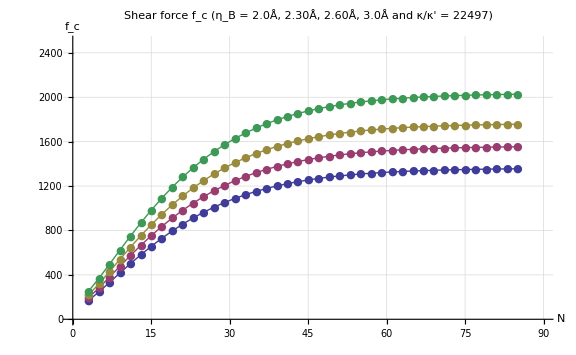

```mathematica
fsTitle=22;
fsAxesLabel=18;
fs2=18;

Show[
{
DataPlots[[1,2]],
DataPlots[[2,2]],
DataPlots[[3,2]],
DataPlots[[4,2]]
},
PlotRange->{{0,90},{0,2500}},
ImageSize->Large,
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AxesOrigin->{0,0},
AxesLabel->{
Style["N",FontSize->fsAxesLabel],
Style["f_c",FontSize->fsAxesLabel]
},
LabelStyle->{"Times",FontSize->fs2},
PlotLabel->Style["Shear force f_c (η_B = "<>
ToString[Round[ToDimension[ToExpression[DataPlots[[1,1]]]],0.1]]<>"0Å, " <>
ToString[Round[ToDimension[ToExpression[DataPlots[[2,1]]]],0.1]]<>"0Å, " <>
ToString[Round[ToDimension[ToExpression[DataPlots[[3,1]]]],0.1]]<>"0Å, " <>
ToString[Round[ToDimension[ToExpression[DataPlots[[4,1]]]],0.1]]<>"0Å and κ/κ' = "<>ToString[κσr]<>")",FontSize->fsTitle]
]
```